```mathematica
om[wl_]:=2Pi*3*^8/(wl*1*^-6)
```

```mathematica
n[wl_]:=Sqrt[3.57-((1.89*^15)^2)/(om[wl]^2+I om[wl]/(6.34*^-15))+(0.49*(5.61*^15)^2)/((5.61*^15)^2-om[wl]^2-I*9.72*^13*om[wl])]
```

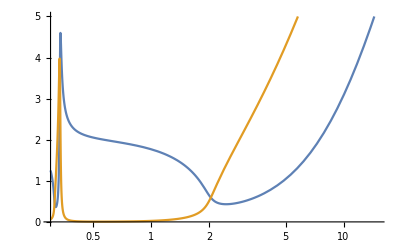

```mathematica
Plot[{Re[n[wl]],Im[n[wl]]},{wl,0.3,15},
PlotRange->{0,5},ScalingFunctions->{"Log",None}]
```

```mathematica
itoData=Import["C:\\Users\\eschl\\Dropbox (MIT)\\MIT\\_Grad\\madmec-2022\\Refractive_indices\\nk_ITO.csv","Data"];
```

```mathematica
itoN=itoData[[2;;,{1,2}]];
itoK=itoData[[2;;,{3,4}]];
```